1.naloga

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

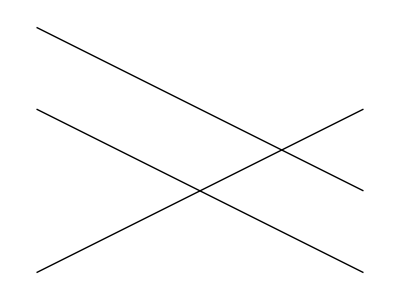

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},{x1, y1}=AA;{x2, y2}=BB;k = (y2 - y1)/(x2 - x1);n =n /.First[Solve[y1 == k*x1 + n, n]];y ==  k*x + n]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
2.naloga
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{resitev},resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},{},First[AA + r(BB - AA) /. resitev]]]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

```mathematica
3.naloga
```

```mathematica
m1={{0,0},{1,1},{0,3},{-1,2}}
m2={{0,0},{1,1},{0,3},{-1,2},{-1,2},{-2,-1},{-1,-1},{0,0}}
Slika[Mnogokotnika[t__]]:=Map[Line,List[t]]
Slika[Mnogokotnika[m1]]
```

{{0,0},{1,1},{0,3},{-1,2}}

{{0,0},{1,1},{0,3},{-1,2},{-1,2},{-2,-1},{-1,-1},{0,0}}

{Line[{{0,0},{1,1},{0,3},{-1,2}}]}

Risanje mnogokotnika

```mathematica
ClearAll[Stranice,Koti, SlikaOglisc, SlikaStranic]
Stranice[{AA_,BB_,CC_, DD_}]:={{AA, BB},{BB,CC},{CC,DD},{DD,AA}}
Koti[{AA_,BB_,CC_, DD_}]:={{DD,AA,BB,CC},{AA,BB,CC,DD},{BB,CC,DD,AA},{CC,DD,AA,BB}}
SlikaOglisc[m1_]:=Map[Point, m1]
SlikaStranic[m1_]:=Map[Line, Stranice[m1]]
```

```mathematica
Stranice[m1]
Koti[m1]
SlikaOglisc[m1]
SlikaStranic[m1]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

{{{-1,2},{0,0},{1,1},{0,3}},{{0,0},{1,1},{0,3},{-1,2}},{{1,1},{0,3},{-1,2},{0,0}},{{0,3},{-1,2},{0,0},{1,1}}}

{Point[{0,0}],Point[{1,1}],Point[{0,3}],Point[{-1,2}]}

{Line[{{0,0},{1,1}}],Line[{{1,1},{0,3}}],Line[{{0,3},{-1,2}}],Line[{{-1,2},{0,0}}]}

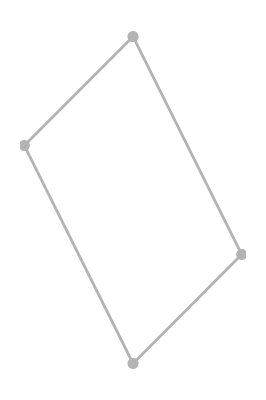

```mathematica
ClearAll[NarisiMnogokotnik]
NarisiMnogokotnik[m1_]:=Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[m1], 
SlikaStranic[m1]}]
NarisiMnogokotnik[m1]
```

```mathematica
Append[m1,{0,0}]
```

{{0,0},{1,1},{0,3},{-1,2},{0,0}}

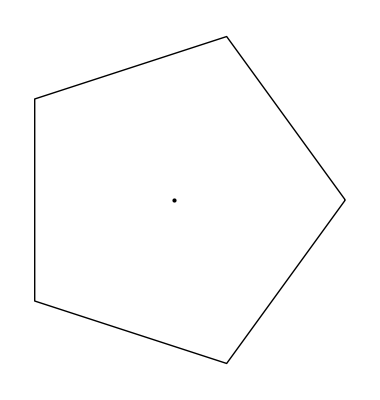

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[Table[{r* Cos[(2Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

```mathematica
PravilniNKotnik[n_,r_, phi_]:= Graphics[{Line[Table[{r*Cos[(2 Pi*i+phi)/n],r*Sin[(2Pi*i+phi)/n]},{i, 0,n}]],Point[{0,0}]}]
pZvezdica =Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

```mathematica
Daljice[Mnogokotnik[t__]]:=Map[Line,Partition[{t},2,1]]
daljice=Daljice[m2]
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

Daljice[{{0,0},{1,1},{0,3},{-1,2},{-1,2},{-2,-1},{-1,-1},{0,0}}]

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
4.naloga
```

Ni pravilna

```mathematica
Presek[m_Mnogokotnikk, d_Daljica]:=Module[{resitev,dal},del=EnacbaNosilke[d];
resitev =Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];]
```

```mathematica
5.naloga
```

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
Outer[f,{1,2,3},{4,5,6}]
Flatten[{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}},1]
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

{f[1,4],f[1,5],f[1,6],f[2,4],f[2,5],f[2,6],f[3,4],f[3,5],f[3,6]}

```mathematica
Flatten - odstrani vse oklepaje znotraj seznama, če pamu dodamo še  argument k odstrani še oklepaje, ki imjo globino manjšo ali enako k.
   Outer - ureja vse možne kombinacije elementov in jih podaja z argumentom f.
```

```mathematica
6.naloga
```

Pokaži, da so vektorji a, b in c komplanarni.

```mathematica
Subscript[v, 1]={-1,3,2}
Subscript[v, 2]={2,-3,-4}
Subscript[v, 3]={-3,12,6}
Cross[Subscript[v, 1], Subscript[v, 2]].Subscript[v, 3]
```

{-1,3,2}

{2,-3,-4}

{-3,12,6}

0